## Multi-Layer Perceptron

```mathematica
netMLP=NetChain[{LinearLayer[5],ElementwiseLayer[Tanh],LinearLayer[1]},"Input"->"Scalar","Output"-> "Scalar"]
```

NetChain[<>]

```mathematica
netMLPinit=NetInitialize[netMLP,Method->{"Random","Biases"->2}]
```

NetChain[<>]

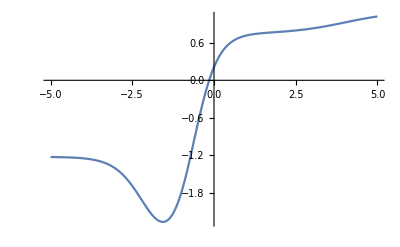

```mathematica
Plot[netMLPinit[x],{x,-5,5}]
```

## NetGraph

```mathematica
graph= NetGraph[{LinearLayer[2],ElementwiseLayer[Tanh],LinearLayer[1],LinearLayer[1]},{1->2->3->NetPort["y"],2->4-> NetPort["z"]},"Input"-> "Scalar","y"-> "Scalar","z"-> "Scalar"]
```

NetGraph[<>]

```mathematica
netInitialized=NetInitialize[graph,Method->{"Random","Biases"->1}]
```

NetGraph[<>]

```mathematica
netInitialized[1]
```

<|y→-0.200876,z→-0.287951|>

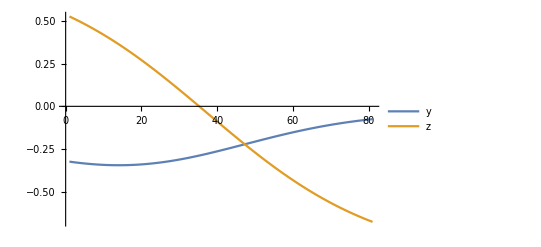

```mathematica
ListLinePlot[netInitialized@Range[-4,4,.1]]
```

## Training